# CoFiAM

### Q Initialization

Define the import folder

```mathematica
Clear["Global`*"];
thisfolder=NotebookDirectory[];
type="KMM";
If[StringSplit[thisfolder,"/"][[Length[StringSplit[thisfolder,"/"]]-0]]=="PDC",pdc=1,pdc=0];
planetnumber=ToExpression[Last[Characters[StringSplit[thisfolder,"/"][[Length[StringSplit[thisfolder,"/"]]-1]]]]];
kic=StringSplit[thisfolder,"/"][[Length[StringSplit[thisfolder,"/"]]-2]];
temp=StringSplit[thisfolder,"/"][[1;;Length[StringSplit[thisfolder,"/"]]-2]];
j=0;datafolder="/";Label[jloop];j=j+1;datafolder=StringJoin[datafolder,temp[[j]],"/"];If[j<Length[temp],Goto[jloop]]
datafolder=StringJoin[datafolder,"RawsLC/"];
Clear[temp];
temp=StringSplit[thisfolder,"/"][[1;;Length[StringSplit[thisfolder,"/"]]-3]];
j=0;rootfolder="/";Label[jloop];j=j+1;rootfolder=StringJoin[rootfolder,temp[[j]],"/"];If[j<Length[temp],Goto[jloop]]
Clear[temp];
```

Import all of the raws....

```mathematica
files=Flatten[Import[StringJoin[datafolder,"files.txt"],"Table"]];
filesLC=Select[files,StringContainsQ[#,"_llc.dat"]&];
filesSC=Select[files,StringContainsQ[#,"_slc.dat"]&];
j=0;Label[jloop];j=j+1;If[pdc==0,Subscript[rawLC, j]=Import[StringJoin[datafolder,filesLC[[j]]],"Table"][[All,{1,2,3,6}]],Subscript[rawLC, j]=Import[StringJoin[datafolder,filesLC[[j]]],"Table"][[All,{1,4,5,6}]]];If[j<Length[filesLC],Goto[jloop]];
j=0;Label[jloop];If[Length[filesSC]==0,Goto[endloop]];j=j+1;If[pdc==0,Subscript[rawSC, j]=Import[StringJoin[datafolder,filesSC[[j]]],"Table"][[All,{1,2,3,6}]],Subscript[rawSC, j]=Import[StringJoin[datafolder,filesSC[[j]]],"Table"][[All,{1,4,5,6}]]];If[j<Length[filesSC],Goto[jloop]];Label[endloop];
```

Import the info file

```mathematica
infofile=Import[StringJoin[rootfolder,type,".dat"],"Table"];
infoline=Select[infofile,#[[1]]==ToExpression[StringSplit[kic,"-"][[2]]]&][[planetnumber]]
```

{9662267,481.886,466.192}

```mathematica
period=infoline[[3]]
tau0=infoline[[2]]+54833
"read duration (only for NEA, else you'll need to mannually input";
duration=period/π ((3π)/(1400*6.674*10^(-11)*(period*86400)^2))^(1/3)
```

466.192

55314.9

0.58787

check how many transits are in the Kepler data, and where

```mathematica
j=0;ntransitsLC=0;Label[jloop];j=j+1;tmin=54833+Min[Subscript[rawLC, j][[All,1]]];tmax=54833+Max[Subscript[rawLC, j][[All,1]]];tabby=Select[Table[tau0+n period,{n,-100,100,1}],tmin<#<tmax&];ntransitsLC=ntransitsLC+Length[tabby];If[Length[tabby]>0,Subscript[activefilesLC, ntransitsLC]=j];If[j<Length[filesLC],Goto[jloop]];
Table[Subscript[activefilesLC, j],{j,1,ntransitsLC}]
ntransitsLC
```

{5,9}

2

```mathematica
j=0;ntransitsSC=0;Label[jloop];If[Length[filesSC]==0,Goto[endloop]];j=j+1;tmin=54833+Min[Subscript[rawSC, j][[All,1]]];tmax=54833+Max[Subscript[rawSC, j][[All,1]]];tabby=Select[Table[tau0+n period,{n,-100,100,1}],tmin<#<tmax&];ntransitsSC=ntransitsSC+Length[tabby];If[Length[tabby]>0,Subscript[activefilesSC, ntransitsLC]=j];If[j<Length[filesSC],Goto[jloop]];Label[endloop];
Table[Subscript[activefilesSC, j],{j,1,ntransitsSC}]
ntransitsSC
```

{}

0

```mathematica
usethisj=Subscript[activefilesLC, 1];
thisraw=Subscript[rawLC, usethisj];
err=Select[thisraw,#[[4]]==0&][[All,{1,2,3}]];
err=Table[{err[[i,1]]+54833,err[[i,2]],err[[i,3]]},{i,1,Length[err]}];
temp=Median[Table[err[[i+1,1]]-err[[i,1]],{i,1,Length[err]-1}]]*24*60;
If[temp>10,sc=0,sc=1];
```

```mathematica
toff=54833;quarter=-1;
exampletime=First[Median[err]];
Q0start=54953.53841518038;Q0end=54963.24481732253;
Q1start=54964.511756673426;Q1end=54997.98329729108;
Q2start=55002.764903284085;Q2end=55091.466956257034;
Q3start=55093.24459723139;Q3end=55182.49465072287;
Q4start=55185.3658080061;Q4end=55275.211866897414;
Q5start=55276.47949780036;Q5end=55371.17207391215;
Q6start=55372.46009847967;Q6end=55462.305792973355;
Q7start=55463.16463513537;Q7end=55552.55707265549;
Q8start=55568.35242605389;Q8end=55635.35368505794;
Q9start=55641.52550915837;Q9end=55738.935875129384;
Q10start=55739.835638486584;Q10end=55833.277845301614;
Q11start=55834.1986379302;Q11end=55931.33445044336;
Q12start=55932.418064826525;Q12end=56015.03062305053;
Q13start=56015.72674011688;Q13end=56106.066162428935;
Q14start=56107.13008618061;Q14end=56204.331588511515;
Q15start=56206.50817485861;Q15end=56304.13718779086;
Q16start=56305.08740097;Q16end=56390.96969746;
If[Q0start<exampletime<Q0end,quarter=0];
If[Q1start<exampletime<Q1end,quarter=1];
If[Q2start<exampletime<Q2end,quarter=2];
If[Q3start<exampletime<Q3end,quarter=3];
If[Q4start<exampletime<Q4end,quarter=4];
If[Q5start<exampletime<Q5end,quarter=5];
If[Q6start<exampletime<Q6end,quarter=6];
If[Q7start<exampletime<Q7end,quarter=7];
If[Q8start<exampletime<Q8end,quarter=8];
If[Q9start<exampletime<Q9end,quarter=9];
If[Q10start<exampletime<Q10end,quarter=10];
If[Q11start<exampletime<Q11end,quarter=11];
If[Q12start<exampletime<Q12end,quarter=12];
If[Q13start<exampletime<Q13end,quarter=13];
If[Q14start<exampletime<Q14end,quarter=14];
If[Q15start<exampletime<Q15end,quarter=15];
If[Q16start<exampletime<Q16end,quarter=16];
If[exampletime>Q16end,quarter=17];
If[quarter==-1,Print["Error quarter unidentified"],Print["quarter ",quarter]]
If[quarter==-1,Speak["Error quarter unidentified"]]
```

quarter 5

```mathematica
Pp=period
τ0=tau0
T14=duration;
Thill=T14*3;
myepoch=0
```

466.192

55314.9

0

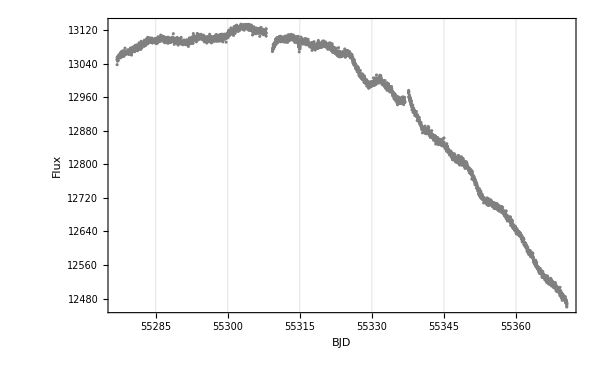

```mathematica
ListPlot[err[[All,{1,2}]],GridLines->{Join[Table[tau0+n period,{n,-100,100,1}],{55018.5,55063.5}],{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray},Axes->None]
```

```mathematica
If[pdc==0,err=Select[err,55310<#[[1]]<55337.25&]];
```

Now plot, adding gridlines for the expected transits

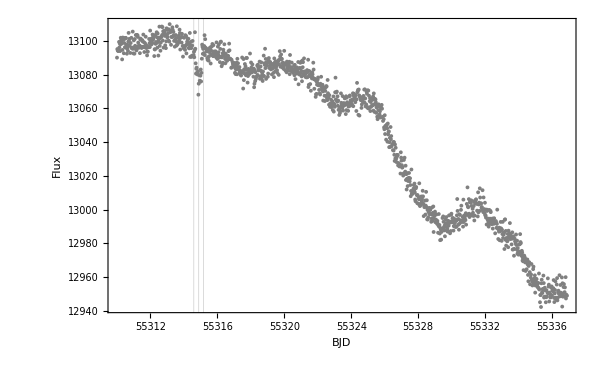

```mathematica
epoch=First[Table[Floor[(Extract[Extract[err,i],1]-τ0)/Pp],{i,1,Length[err]}]]+1;
ListPlot[err[[All,{1,2}]],GridLines->{{tau0,tau0-0.5T14,tau0+0.5T14},{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray},Axes->None]
```

Now exclude transits...

```mathematica
gap=0.5T14+N[0.5/24];
temp=err;
phase=Table[Extract[Extract[err,i],1]-Pp Floor[(Extract[Extract[err,i],1]-τ0)/Pp]-τ0,{i,1,Length[err]}];
phase=Table[(Extract[phase,i]/Pp)-Round[(Extract[phase,i]/Pp)],{i,1,Length[phase]}];
n=0;Label[nloop];n=n+1;ϕmax=gap/Pp;j=0;m=0;Label[jloop];j=j+1;If[Abs[Extract[phase,j]]>ϕmax,m=m+1];If[Abs[Extract[phase,j]]>ϕmax,Subscript[α, m]=Extract[temp,j]];If[j<Length[temp],Goto[jloop]];mmax=m;Print["For transit number ",n,", ",mmax," points out of ",Length[temp]," are accepted"];temp=Table[Subscript[α, mm],{mm,1,mmax}];If[n<1,Goto[nloop]];
out=temp;
```

For transit number 1, 1226 points out of 1256 are accepted

Now accept temp as the out-of-transits array...

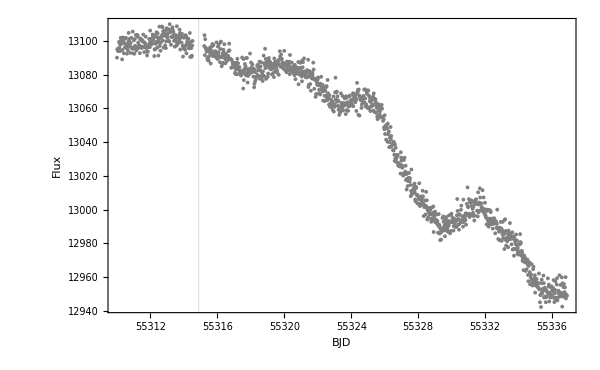

```mathematica
out=temp;
outlist=Table[{Extract[Extract[out,i],1],Extract[Extract[out,i],2]},{i,1,Length[out]}];
ListPlot[outlist,GridLines->{{τ0+epoch Pp},{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray},Axes->None]
```

### Outlier rejection for Q

Q3 is relatively simple to clean.
There are no jumps or exponential rises.
We can therefore skip straight to outlier rejection followed by cosine filter.

InterpolatingFunction::dmval: Input value {55310.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

12942.2

13110.

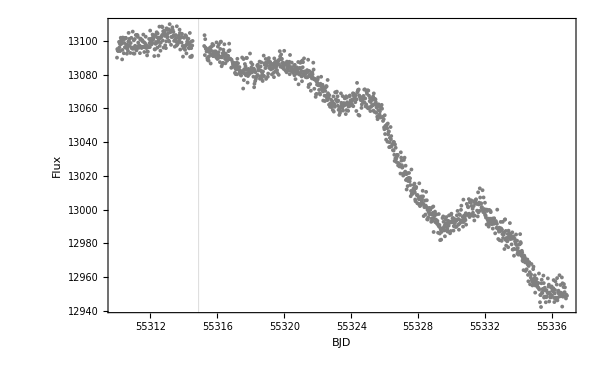

5 points removed

```mathematica
bin=20;
sigma=3;
smoothfn=Interpolation[MovingMedian[outlist,bin],InterpolationOrder->1];
res=Table[{Extract[Extract[out,i],1],Extract[Extract[out,i],2]-smoothfn[Extract[Extract[out,i],1]],Extract[Extract[out,i],3]},{i,1,Length[out]}];
j=0;m=0;Label[jloop];j=j+1;If[Abs[Extract[Extract[res,j],2]/Extract[Extract[res,j],3]]<sigma,m=m+1];If[Abs[Extract[Extract[res,j],2]/Extract[Extract[res,j],3]]<sigma,Subscript[γ, m]=Extract[out,j]];If[j<Length[res],Goto[jloop]];mmax=m;
nice=Table[Subscript[γ, mm],{mm,1,mmax}];
nicelist=Table[{Extract[Extract[nice,i],1],Extract[Extract[nice,i],2]},{i,1,Length[nice]}];
fluxmin=Last[First[Sort[nicelist,#1[[2]]<#2[[2]]&]]]
fluxmax=Last[Last[Sort[nicelist,#1[[2]]<#2[[2]]&]]]
ListPlot[nicelist,GridLines->{{τ0+epoch Pp},{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray},Axes->None]
Print[Length[out]-Length[nice]," points removed"]
```

## localpoly

### Filter Q

Pdur is the timescale which you protect. I have chosen this to be equal to the maximum transit duration. However, there is an argument for using twice this value as well.

```mathematica
training=Select[nice,τ0+epoch Pp-2Thill≤#[[1]]≤τ0+epoch Pp+2Thill&];
nmax = Min[30,Length[training]-1];
nmin = 0;
```

```mathematica
n=nmin-1;Label[nloop];n=n+1;"REGRESS";weiQ = Table[Extract[Extract[training, i], 3]^(-2), {i,1,Length[training]}];t0=First[Mean[training]];lmQ= LinearModelFit[training[[All,{1,2}]],Table[(t-t0)^k,{k,1,n}],t,Weights->weiQ];bic=N[Sum[((training[[i,2]]-lmQ[training[[i,1]]])/training[[i,3]])^2,{i,1,Length[training]}]+n Log[Length[training]]];Subscript[ζζ, n]={n,bic};Print[{n,bic}];If[n<nmax,Goto[nloop]];"DONE!";
```

{0,1511.81}

{1,524.186}

{2,369.179}

{3,352.636}

{4,357.719}

{5,362.865}

{6,354.114}

{7,351.415}

{8,349.914}

{9,355.618}

{10,361.317}

{11,365.306}

{12,365.469}

{13,368.069}

{14,373.084}

{15,376.52}

{16,382.007}

{17,386.798}

{18,392.496}

{19,397.836}

{20,403.326}

{21,408.205}

{22,411.903}

{23,416.676}

{24,422.147}

{25,424.458}

{26,425.455}

{27,431.145}

{28,436.825}

{29,440.959}

{30,445.696}

```mathematica
results=Sort[Table[{Subscript[ζζ, nn][[2]],Subscript[ζζ, nn][[1]]},{nn,1,nmax}]]
```

{{349.914,8},{351.415,7},{352.636,3},{354.114,6},{355.618,9},{357.719,4},{361.317,10},{362.865,5},{365.306,11},{365.469,12},{368.069,13},{369.179,2},{373.084,14},{376.52,15},{382.007,16},{386.798,17},{392.496,18},{397.836,19},{403.326,20},{408.205,21},{411.903,22},{416.676,23},{422.147,24},{424.458,25},{425.455,26},{431.145,27},{436.825,28},{440.959,29},{445.696,30},{524.186,1}}

### apply optimal

```mathematica
n=Last[First[results]];
weiQ = Table[Extract[Extract[training, i], 3]^(-2), {i,1,Length[training]}];
t0=First[Mean[training]];
man=LinearModelFit[training[[All,{1,2}]],Table[(t-t0)^k,{k,1,n}],t,Weights->weiQ]//Timing
lmQ=Extract[man,2];
```

{0.009817,FittedModel[13094.6-2.52355 (-55314.9+t)+«11»]}

```mathematica
missing=Select[err[[All,{1,2}]],!MemberQ[nicelist,#]&];
```

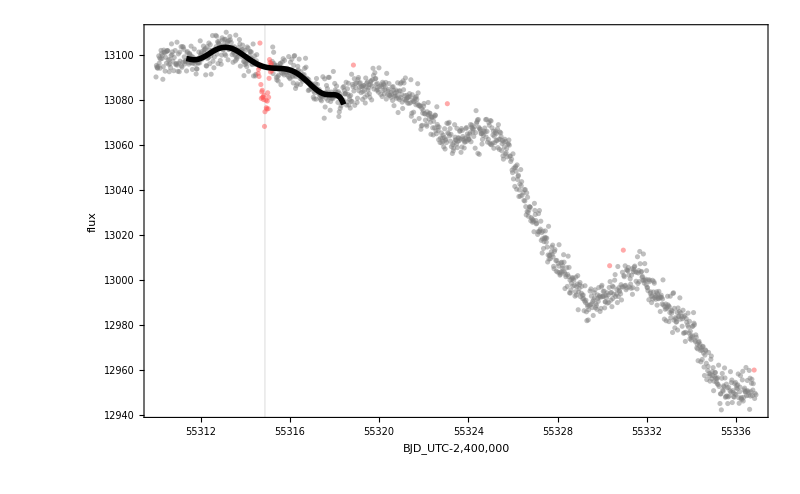

```mathematica
Qplot=Show[{ListPlot[{nicelist,missing},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[Lighter[Red],Opacity[0.5]]},Frame->True,FrameLabel->{"BJD_UTC-2,400,000","flux"},ImageSize->{800,550},BaseStyle->{FontFamily->"SF Pro Display",FontSize->24},Axes->None,PlotRange->{{Min[err[[All,1]]],Max[err[[All,1]]]},All}], 
 Plot[lmQ[t], {t, τ0+epoch Pp-2Thill,τ0+epoch Pp+2Thill},PlotStyle->{Black, Thickness[0.005]}]},Frame->True,Axes->None,GridLines->{{τ0+epoch Pp},{}},PlotRange->{{Min[err[[All,1]]],Max[err[[All,1]]]},All}]
```

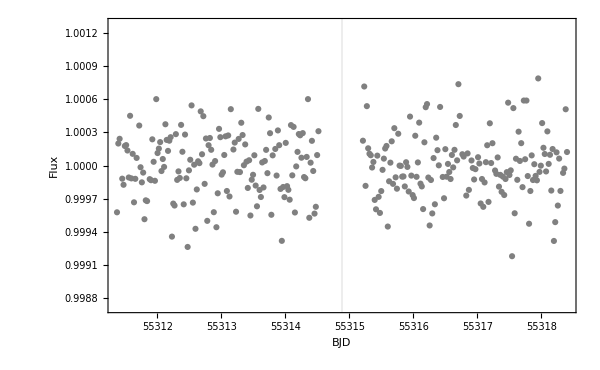

Standard deviation ~ 256.214 ppm

```mathematica
test=Table[lmQ[Extract[Extract[training,i],1]],{i,1,Length[training]}];
super=Table[{Extract[Extract[training,i],1],Extract[Extract[training,i],2]/Extract[test,i],Extract[Extract[training,i],3]/Extract[test,i]},{i,1,Length[training]}];
superlist=Table[{Extract[Extract[super,i],1],Extract[Extract[super,i],2]},{i,1,Length[super]}];
scatter=1.4286*Extract[MedianDeviation[super],2];
ListPlot[superlist,GridLines->{{τ0+epoch Pp},{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray},Axes->None,Joined->{False},PlotRange->{{First[First[superlist]],First[Last[superlist]]},{1-5*scatter,1+5*scatter}}]
Print["Standard deviation ~ ",scatter*10^6," ppm"]
```

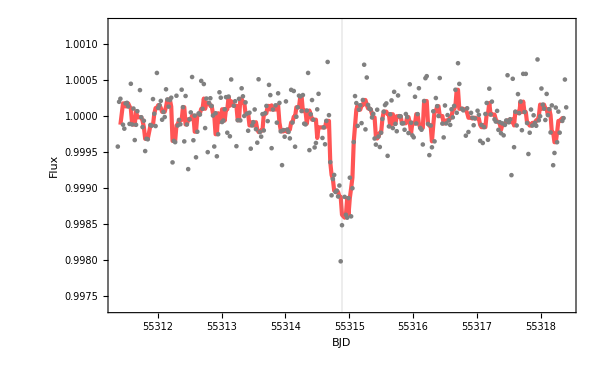

Standard deviation ~ 266.131 ppm

```mathematica
err2=Select[err,τ0+epoch Pp-2Thill≤#[[1]]≤τ0+epoch Pp+2Thill&];
test2=Table[lmQ[Extract[Extract[err2,i],1]],{i,1,Length[err2]}];
gud=Table[{Extract[Extract[err2,i],1],Extract[Extract[err2,i],2]/Extract[test2,i],Extract[Extract[err2,i],3]/Extract[test2,i]},{i,1,Length[err2]}];
gudlist=Table[{Extract[Extract[gud,i],1],Extract[Extract[gud,i],2]},{i,1,Length[gud]}];
"START OF MIN FLUX ESTIMATOR";
j=0;m=0;Label[jloop];j=j+1;If[τ0+epoch Pp-0.25T14<Extract[Extract[gudlist,j],1]<τ0+epoch Pp+0.25T14,m=m+1];If[τ0+epoch Pp-0.25T14<Extract[Extract[gudlist,j],1]<τ0+epoch Pp+0.25T14,Subscript[μζ, m]=Extract[gudlist,j]];If[j<Length[gudlist],Goto[jloop]];
surround=Table[Subscript[μζ, mm],{mm,1,m}];surround=Table[{Extract[Extract[surround,i],1]-(τ0+epoch Pp),Extract[Extract[surround,i],2]},{i,1,Length[surround]}];
polyfit=NonlinearModelFit[surround,a+c t^2,{a,c},t];
minflux=polyfit[0];
"END OF MIN FLUX ESTIMATOR";
If[sc==0,smoothinteger=5,smoothinteger=30];
ListPlot[{gudlist,MovingMedian[gudlist,smoothinteger]},GridLines->{{τ0+epoch Pp},{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray,{Lighter[Red],Thickness[0.005]}},PlotRange->{{τ0+epoch Pp-2Thill,τ0+epoch Pp+2Thill},{minflux-5*scatter,1+5 scatter}},Axes->None,Joined->{False,True}]
Print["Standard deviation ~ ",1.4286*Extract[MedianDeviation[gud],2]*10^6," ppm"]
```

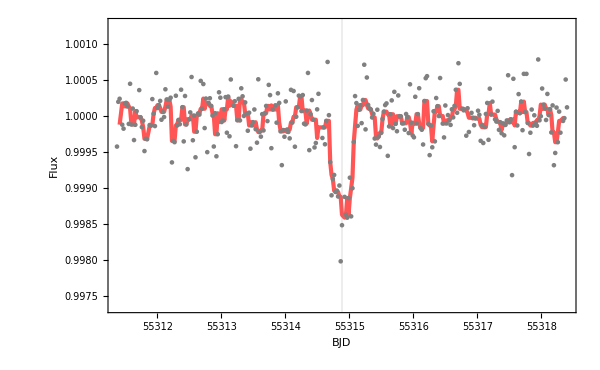

```mathematica
ListPlot[{gudlist,MovingMedian[gudlist,smoothinteger]},GridLines->{{τ0+epoch Pp},{}},Frame->True,BaseStyle->{"Times",16},FrameLabel->{"BJD","Flux"},ImageSize->{600,400},PlotStyle->{Gray,{Lighter[Red],Thickness[0.005]}},PlotRange->{{First[First[gud]],First[Last[gud]]},{minflux-5*scatter,1+5 scatter}},Axes->None,Joined->{False,True}]
```

```mathematica
phase=Table[Extract[Extract[gud,i],1]-Pp Floor[(Extract[Extract[gud,i],1]-τ0)/Pp]-τ0,{i,1,Length[gud]}];
phase=Table[(Extract[phase,i]/Pp)-Round[(Extract[phase,i]/Pp)],{i,1,Length[phase]}];
j=0;m=0;Label[jloop];found=0;j=j+1;If[Abs[Extract[phase,j]]≤N[(2Thill)/Pp],found=1];If[found==1,m=m+1];If[found==1,Subscript[Δ, m]=Extract[gud,j]];If[j<Length[gud],Goto[jloop]];
m
```

330

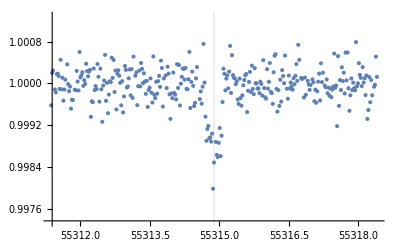

```mathematica
myQ=Table[Subscript[Δ, mm],{mm,1,m}];
myQlist=Table[{Extract[Extract[myQ,i],1],Extract[Extract[myQ,i],2]},{i,1,Length[myQ]}];
ListPlot[myQlist,PlotRange->{{τ0+epoch Pp-2Thill,τ0+epoch Pp+2Thill},{minflux-5*scatter,1+5 scatter}},GridLines->{{τ0+epoch Pp},{}}]
```

```mathematica
If[sc==0,bin=5,bin=30];
If[sc==0,sigma=100,sigma=3];
smoothfn=Interpolation[MovingMedian[myQlist,bin],InterpolationOrder->1];
res=Table[{Extract[Extract[myQ,i],1],Extract[Extract[myQ,i],2]-smoothfn[Extract[Extract[myQ,i],1]],Extract[Extract[myQ,i],3]},{i,1,Length[myQ]}];
j=0;m=0;Label[jloop];j=j+1;If[Abs[Extract[Extract[res,j],2]/Extract[Extract[res,j],3]]<sigma,m=m+1];If[Abs[Extract[Extract[res,j],2]/Extract[Extract[res,j],3]]<sigma,Subscript[γ, m]=Extract[myQ,j]];If[j<Length[res],Goto[jloop]];mmax=m;
myQ2=Table[Subscript[γ, mm],{mm,1,mmax}];
myQ2list=Table[{Extract[Extract[myQ2,i],1],Extract[Extract[myQ2,i],2]},{i,1,Length[myQ2]}];
Print[Length[myQ]-Length[myQ2]," points rejected"]
ListPlot[myQ2list,PlotRange->{{τ0+epoch Pp-2Thill,τ0+epoch Pp+2Thill},{minflux-5*scatter,1+5 scatter}},GridLines->{{τ0+epoch Pp},{}}]
```

InterpolatingFunction::dmval: Input value {55311.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {55318.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0 points rejected

-Graphics-

```mathematica
phasex=Table[Extract[Extract[myQ2,i],1]-Pp Floor[(Extract[Extract[myQ2,i],1]-τ0)/Pp]-τ0,{i,1,Length[myQ2]}];
phasex=Table[(Extract[phasex,i]/Pp)-Round[(Extract[phasex,i]/Pp)],{i,1,Length[phasex]}];
```

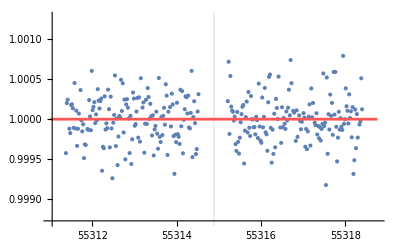

```mathematica
j=0;m=0;Label[jloop];found=0;j=j+1;If[N[gap/Pp]≤Abs[Extract[phasex,j]]≤N[(2Thill)/Pp],found=1];If[found==1,m=m+1];If[found==1,Subscript[φ, m]=Extract[myQ2,j]];If[j<Length[myQ2],Goto[jloop]];
baseQ=Table[Subscript[φ, mm],{mm,1,m}];
baseQlist=Table[{Extract[Extract[baseQ,i],1],Extract[Extract[baseQ,i],2]},{i,1,Length[baseQ]}];
linfit=LinearModelFit[baseQlist,x,x,Weights->Table[Extract[Extract[baseQ,i],3]^(-2),{i,1,Length[baseQ]}]];
Show[ListPlot[baseQlist,PlotRange->{{τ0+epoch Pp-2.2Thill,τ0+epoch Pp+2.2Thill},{1-5*scatter,1+5 scatter}},GridLines->{{τ0+epoch Pp},{}}],Plot[linfit[x],{x,τ0+epoch Pp-2.2Thill,τ0+epoch Pp+2.2Thill},PlotStyle->{Lighter[Red],Thickness[0.005]}]]
```

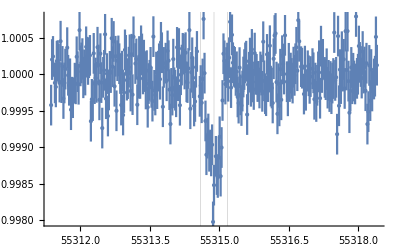

```mathematica
myQ3=Table[{Extract[Extract[myQ2,i],1],Extract[Extract[myQ2,i],2]/linfit[Extract[Extract[myQ2,i],1]],Extract[Extract[myQ2,i],3]/linfit[Extract[Extract[myQ2,i],1]]},{i,1,Length[myQ2]}];
<<ErrorBarPlots`
ErrorListPlot[myQ3,PlotRange->{{τ0+epoch Pp-2Thill,τ0+epoch Pp+2Thill},All},GridLines->{{τ0+epoch Pp,τ0+epoch Pp-0.5T14,τ0+epoch Pp+0.5T14},{}}]
```

```mathematica
If[pdc==1,file=StringJoin["localPDC.Q",ToString[quarter],".dat"],file=StringJoin["localSAP.Q",ToString[quarter],".dat"]];
If[Length[myQ]>0,Export[StringJoin[thisfolder,file],myQ3,"Table"],Print["No data"]]
```

/Users/dkipping/Storage1/Work/Documents/Transit_Work/PAPERS/Cool_KOIs/KMM/KIC-9662267/planet1/SAP/localSAP.Q5.dat

```mathematica
Speak["CoFiAM complete"]
```